# ALLA SCOPERTA DELLA TRIGONOMETRIA

```mathematica
Import["ImmagineGruppo.jpeg"]
```

-Graphics-

## Calcolo Numerico e Software Didattico - Matematica Computazionale Gianluca Lutero - Filippo Soncini - Adele Valerii - Sara Gattari Anno Accademico 2016-2017 NB. Per andare avanti clicca sulla freccia in alto e clicca sul bottone “Carica Package” nella prossima slide.

```mathematica
Button["Carica Package ",SetDirectory[NotebookDirectory[]];
<< Trigonometria.m;
FrontEndExecute[FrontEndToken[InputNotebook[],"EvaluateInitialization"]];
FrontEndExecute[FrontEndToken[InputNotebook[],"SelectAll"]];
FrontEndExecute[FrontEndToken[InputNotebook[],"EvaluateCells"]];
]
```

Carica Package

## Regole

-Gli angoli sono indicati con le lettere greche: α, β, θ, δ, γ.

Teoria
- Quando vedi un pulsante clicca sopra per scoprire nuove cose;
- Per vedere cosa accade prova a muovere i punti nei disegni (se premi il pulsante + puoi avviare le animazioni).

Esercizi
- Negli esercizi non troverai il testo scritto, ma l’immagine del problema con relativi dati scritti a fianco;
- Usa sempre le lettere maiuscole per indicare i lati;
- Schiaccia invio per confermare ciò che hai inserito;
- Il seno è indicato con sen, il coseno è indicato con cos, la tangente è indicata con tan;
- Negli esercizi guidati leggi i suggerimenti e completa di conseguenza all’interno delle caselle;
- Negli esercizi a risposta multipla clicca sul pallino della risposta che secondo te è corretta;
- Il simbolo / significa “fratto” o ”diviso”;
- Puoi usare una calcolatrice.

## Obiettivi - Apprendere i principali teoremi della trigonometria con facilità e divertimento: - Definizioni di Seno, Coseno e Tangente - Teorema della corda - Teorema dei seni - Teorema del coseno - Rendere i concetti facimente comprensibili agli alunni con disturbi specifici dell’apprendimento (DSA). - Infine, tramite gli esercizi guidati dare la possibilità allo studente di mettersi alla prova.

## A chi è rivolto

- Studenti del terzo anno della Scuola Secondaria di Secondo Grado.
- Le definizioni possono essere adatte anche agli studenti del primo anno della Scuola Secondaria di Secondo Grado, in quanto ne hanno necessità per l’applicazione alla fisica.

## Prerequisiti

- Nozioni algebriche:

```mathematica
Button[Style["Prerequisiti algebra",FontFamily->"OpenDyslexic"],MessageDialog[Style["Operazioni con i polinomi;\nOperazioni con le frazioni;\nProdotti notevoli;\nRaccoglimento a fattor comune;\nApprossimazione dei numeri decimali.",FontFamily->"OpenDyslexic"],WindowSize->All,Editable->False]]
```

Prerequisiti algebra

-Nozioni geometriche:

```mathematica
Button[Style["Prerequisiti geometria",FontFamily->"OpenDyslexic"],MessageDialog[Style["Teorema di Pitagora;\nCriteri di congruenza dei triangoli;\nCriteri di similitudine dei triangoli;\nProprietà degli angoli alla circonferenza: tutti gli angoli che insistono sullo stesso arco sono uguali;\nProprietà dei triangoli inscritti in una circonferenza:i triangoli inscritti in una semicirconferenza sono rettangoli;\nProprietà dei poligoni inscritti e circoscritti ad un circonferenza;\nSomma degli angoli interni ad un triangolo.",FontFamily->"OpenDyslexic"],WindowSize->All,Editable->False]]
```

Prerequisiti geometria

-Nozioni goniometriche:

```mathematica
Button[Style["Prerequisiti goniometria",FontFamily->"OpenDyslexic"],MessageDialog[Style["Funzioni goniometriche (seno,coseno,tangente);\nFunzioni inverse (arcoseno,arcocoseno, arcotangente);\nAngoli associati.",FontFamily->"OpenDyslexic"],WindowSize->All,Editable->False]]
```

Prerequisiti goniometria

## DEFINIZIONI: SENO e COSENO

Data una circonferenza di centro l’origine e raggio 1, indicato con θ l’angolo indiduato dall’asse delle ascisse e da una semiretta con orinigne nel centro della circonferenza, chiamiamo P il punto di intersezione tra la circonferenza e questa semiretta.

Il seno dell’angolo è l’ordinata del punto P                 sen(θ) = y_P
Il coseno dell’angolo è l’ascissa del punto P               cos(θ) = x_P

```mathematica
defsencos[]
```

```mathematica
bottonesen[]
```

Funzione Seno

```mathematica
bottonecos[]
```

Funzione Coseno

Osserva che OPH è un triangolo rettangolo

sen(θ) = y_P = OverBar[PH] = OverBar[PH]/1 = OverBar[PH]/OverBar[OP]
cos(θ) = x_P = OverBar[OH] = OverBar[OH]/1 = OverBar[OH]/OverBar[OP]

```mathematica
rapporti[]
```

sen(θ) = (CATETO OPPOSTO ALL'ANGOLO θ)/IPOTENUSA = OverBar[AB]/OverBar[AC]   cos(θ) = (CATETO ADIACENTE ALL'ANGOLO θ)/IPOTENUSA =OverBar[BC]/OverBar[AC]

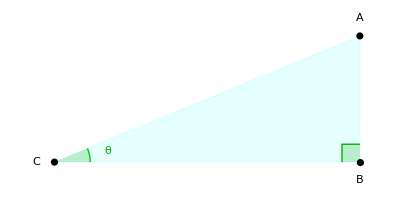

```mathematica
triangolorett[]
```

Il triangolo ABC è rettangolo quindi posso applicare il teorema di Pitagora: OverBar[AB]^2+OverBar[BC]^2=OverBar[AC]^2  

dividiamo tutto per OverBar[AC]^2, otteniamo OverBar[AB]^2/OverBar[AC]^2+OverBar[BC]^2/OverBar[AC]^2=OverBar[AC]^2/OverBar[AC]^2 che è uguale (guardando le formule di seno e coseno) a: 

sen^2(θ) + cos^2(θ) = 1. Questa è la formula fondamentale della trigonometria!

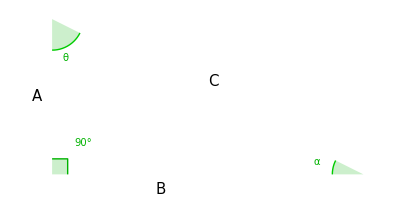
Esempio 1: |  | 
-Graphics- | A = 25 
C = 50
Trovare sen(α) | 
Procedimento: |  | 
  |  Sin(α) = A/C = 25/50 = 1/2 |

```mathematica
EsercizioEsempio[]// Quiet
```

## DEFINIZIONI: TANGENTE

Chiamiamo T il punto di intersezione tra la semiretta su cui giace OverBar[OP] e la retta passante per K=(1,0) e perpendicolare all’asse x.

tan(θ)=y_T

```mathematica
definizionetangente[]
```

I triangoli POH e TKO sono simili, infatti essi hanno:  
	-θ in comune
	-sono entrambi rettangoli
	-per differenza anche il terzo angolo è uguale (la somma degli angoli interni ad un triangolo è 180°)

Essendo simili il rapporto tra i lati è lo stesso:          

OverBar[TK]/OverBar[PH] = OverBar[OK]/OverBar[OH] ⟶ OverBar[TK]/(sen(θ)) = OverBar[OK]/(cos(θ))      OK è 1 perchè è il raggio della circonferenza, da cui    

OverBar[TK]/(sen(θ)) = 1/(cos(θ)) ⟶ OverBar[TK] = (sen(θ))/(cos(θ)) e si nota dalla figura che OverBar[TK] è proprio la y_T. Quindi:

tan(θ) = (sen(θ))/(cos(θ))

```mathematica
bottonetan[]
```

Funzione Tangente

## ANGOLI NOTI

Osserva i valori di seno, coseno e tangente dei principali angoli.
In questa animazione puoi osservare seno, coseno e tangente degli angoli che sono multipli di 30°.
Per cambiare angolo muovi il cursore blu!

```mathematica
angolinoti30[]
```

In questa animazione puoi osservare seno, coseno e tangente degli angoli multipli di 45°.
Per cambiare angolo muovi il cursore blu!

```mathematica
angolinoti45[]
```

Osserva che il seno di un angolo è uguale al seno del suo supplementare: ad esempio il seno di 30° è uguale al seno di 150°. Questo ti servirà in una slide dopo.

## Promemoria: FORMULE INVERSE

Come trovo l’angolo θ a partire dal seno?
sen(θ) = 1/2 ⟶ θ ?
θ = arcsen(1/2) = sen^-1(1/2) = 30°    ⟷    30° è l’angolo che ha come seno 1/2
L’arcoseno è la formula inversa del seno!

Come trovo l’angolo θ a partire dal coseno?
cos(θ)  = (√3)/2 ⟶ θ ?
θ = arccos((√3)/2) = cos^-1((√3)/2) = 30°    ⟷    30° è l’angolo che ha come coseno (√3)/2
L’arcocoseno è la formula inversa del coseno!

Come trovo l’angolo θ a partire dalla tangente?
tan(θ) = 1/(√3) ⟶ θ ?
θ = arctan(1/(√3)) = tan^-1(1/(√3)) = 30°    ⟷    30° è l’angolo che ha come tangente (√3)/2
L’arcotangente è la formula inversa della tangente!

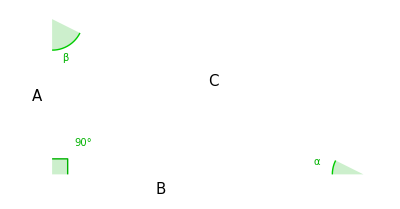
Esercizio Guidato: |  | 
-Graphics- | A = 40 
B = 110
Trovare sen(α),cos(α),tan(α) e l'angolo α | 
Procedimento: |  | 
Passo 1: Cerchiamo l'ipotenusa C.
 Applico il Teorema di Pitagora: |  | 
 | Teorema di Pitagora
Applico il teorema ⟶ A^2 + ^2  = ^2
 
Sostituisco i valori ⟶ 40^2 + ^2  = C^2

Ricavo C ⟶ C = √(A^2 + ^2)
 
Approssima il risultato per difetto!

Calcolo C ⟶ C = √(^2 + ^2) =  | 
Passo 2: Cerchiamo sen(α).
Attenzione: nei passaggi,
prima sostituisci le lettere,
poi i valori corrispondenti. |  | 
 | sen(α) = A/ = 40/ | 
Passo 3: Cerchiamo cos(α). |  | 
 | cos(α) = B/ = 110/ | 
Passo 4: Cerchiamo tan(α). |  | 
 | tan(α) = (α)/(cos(α))
Sostituisco i valori di seno e coseno trovati ai passi 2 e 3: ///
Ricorda! La divisione tra due frazioni
diventa la prima frazione moltiplicata per l'inversa della seconda:/·/
Dopo aver eseguito la moltiplicazione tra le due frazioni ottengo:/
Semplifico ai minimi termini la frazione e ottengo:/ | 
Passo 5: Cerchiamo α. |  | 
 | α = sen^-1(/) |

```mathematica
Esercizio1[]// Quiet
```

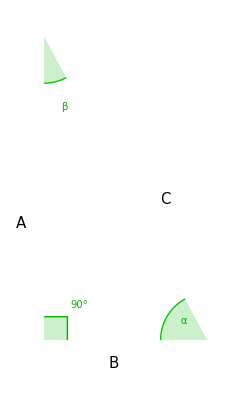
Esercizio 2: |  | 
-Graphics- | B = 30 
tan(β) = 3/5
Trovare A | 
Procedimento: |  | 
Ricorda! tanβ =(cateto opposto)/(cateto adiacente) |  | 
Qual è il cateto adiacente? |  | A   | B   | C | 
Qual è il cateto opposto? |  | A   | B   | C | 
Completa i passaggi
ed osserva i suggerimenti proposti:  |  | 
tanβ = /    ⟶    A·tan(β) = B    ⟶    A = B/(tan (β)) |  | 
Quanto vale A? |  | 50   | 18   | 2 |

```mathematica
Esercizio2[]// Quiet
```

## TEOREMA DELLA CORDA

Presa una qualunque circonferenza ed una sua qualunque corda si ha:

### OverBar[AB] = 2r·sen(θ)

dove θ è l’angolo alla circonferenza che insiste sulla corda OverBar[AB].

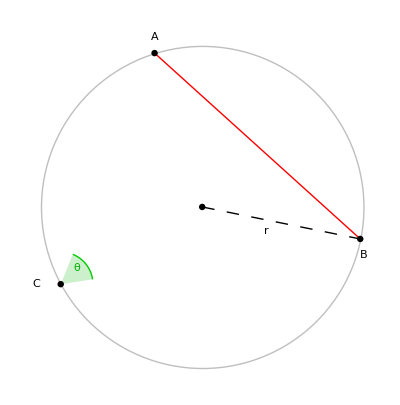
-Graphics- |

```mathematica
teoremacorda[]
```

#### DIMOSTRAZIONE

```mathematica
teoremacorda2[]
```

Muovi C lungo l’arco viola!

Cosa puoi notare? L’angolo θ ha sempre la stessa ampiezza!

Perchè? Perchè è un angolo alla circonferenza che insiste sulla corda OverBar[AB] (ricorda che tutti gli angoli che insistono sulla stessa corda sono uguali).

Quindi possiamo posizionare il punto C in modo tale che OverBar[AC] passi per il centro della circonferenza e corrisponda al diametro così il triangolo ABC è rettangolo in B (ricorda che qualunque triangolo inscritto in una semiscirconferenza lo è). 
Ora possiamo applicare le formule che abbiamo visto prima! 
 
OverBar[AC] = 2r è l’ipotenusa e AB è il cateto opposto a θ, quindi, considerando che sen(θ)=OverBar[AB]/OverBar[AC] si ha:
OverBar[AB] = OverBar[AC] ·sen(θ) = 2r·sen(θ)

Quindi OverBar[AB] = 2r·sen(θ).

Questa formula vale sempre perché θ è sempre lo stesso! 

Quando l’angolo è nell’arco rosa cosa succede?
Prova a muovere D lungo l’arco rosa!
Anche l’angolo δ ha sempre la stessa ampiezza perchè è un angolo alla circonferenza che insiste sulla corda OverBar[AB].

```mathematica
teoremacorda3[]
```

ADBC è un poligono inscritto nella circonferenza quindi gli angoli opposti sono supplementari, cioè: δ=π-θ.
I seni sono gli stessi, infatti sen(α) = sen(π-α) (vedi slide 9). 
Quindi anche considerando l’arco rosa la formula resta la stessa!!!

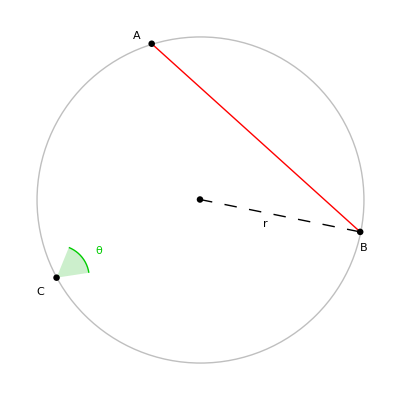
Esercizio 3: | 
-Graphics- | r = 2
θ = 60^o
Trovare OverBar[AB]
Procedimento: | 
OverBar[AB] = 2·  · sen(^o) = ·√/ =  ·√ |

```mathematica
Esercizio3[]// Quiet
```

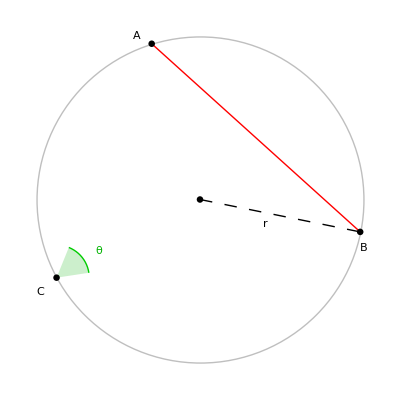
Esercizio 4: |  | 
-Graphics- | r = 5
θ = 60^o
Trovare OverBar[AB] | 
Quindi il lato OverBar[AB] misura: |  | 5/2   | 5/2√3   | 5\*SqrtBox[\(3\)]   | 30 |

```mathematica
Esercizio4[]// Quiet
```

## TEOREMA DEI SENI

Dato un triangolo ABC qualsiasi:

OverBar[BC]/(sen(α)) = OverBar[AC]/(sen(β))= OverBar[AB]/(sen(θ))

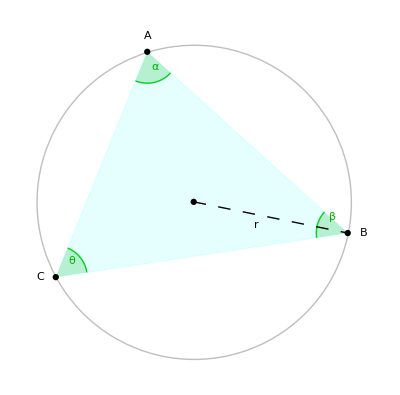

```mathematica
teoremaseni[]
```

### DIMOSTRAZIONE

```mathematica
teoremaseni[]
```

-Graphics-

Direttamente dal teorema della corda:
OverBar[BC] = 2r·sen(α) ⟶ OverBar[BC]/(sen(α)) = 2r
OverBar[AC] = 2r·sen(β) ⟶OverBar[AC]/(sen(β))= 2r
OverBar[AB] = 2r·sen(θ)⟶ OverBar[AB]/(sen(θ)) = 2r

Quindi:

OverBar[BC]/(sen(α)) = OverBar[AC]/(sen(β))= OverBar[AB]/(sen(θ))

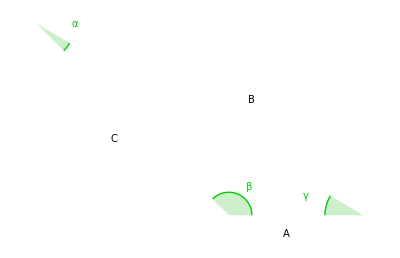
Esercizio 5: |  | 
-Graphics- | A = 6 
α = 30^o
β = 105^o
Trovare C | 
Procedimento: |  | 
Calcolare l'ampiezza dell'angolo γ: 180^o-(^o+^o) = ^o |  | 
Utilizzare la relazione A/(sen (α)) =C/(sen (γ)) |  | 
 | 6/(sen(^o)) = /(sen(45^o)) ⟶  6 / / =  /SqrtBox[2]/2 | 
Ricavare: |  | 
 | C = 6√/ / / = √ |

```mathematica
Esercizio5[]// Quiet
```

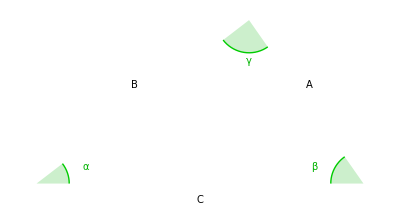
Esercizio 6: |  | 
-Graphics- | A = 12 
B = 9
β = 30^o
Trovare sen(α) | 
Procedimento: |  | 
Ricorda! A/(sen (α)) =B/(sen (β)) =C/(sen (γ)) |  | 
Quanto misura sen(α)? |  | 3/2   | 2/3   | 2/3√3   | 3/2√3 |

```mathematica
Esercizio6[]// Quiet
```

## TEOREMA DEL COSENO (o di CARNOT)

Dato un triangolo ABC qualunque:

### OverBar[AB]^2 = OverBar[AC]^2+OverBar[CB]^2-2·OverBar[CB]·OverBar[AC]·cos(γ)

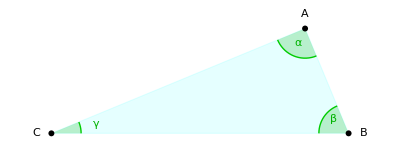

```mathematica
teoremacoseno[]
```

```mathematica
bottonepitagora[]
```

Teorema di Pitagora

### DIMOSTRAZIONE

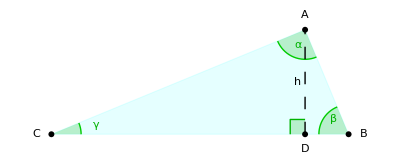

```mathematica
teoremacoseno2[]
```

Guardando il triangolo ADC: 
dalle formule cos(γ)=OverBar[CD]/OverBar[AC] e sen(γ)=OverBar[AD]/OverBar[AC] si ottiene

OverBar[CD] = OverBar[AC]·cos(γ)
OverBar[AD] = OverBar[AC]·sen(γ)

Per costruzione: OverBar[DB] = OverBar[CB]-OverBar[CD] = OverBar[CB]-OverBar[AC]·cos(γ)
Applichiamo il teorema di Pitagora al triangolo ADB:

OverBar[AB]^2 = OverBar[DB]^2+OverBar[AD]^2 = (OverBar[CB]-OverBar[AC]·cos(γ))^2+(OverBar[AC]·sen(γ))^2

Sviluppiamo il quadrato del binomio: OverBar[CB]^2+OverBar[AC]^2·cos^2(γ)-2OverBar[CB]·OverBar[AC]·cos(γ)+OverBar[AC]^2·sen^2(γ) 
 
e raccogliamo a fattor comune il termine OverBar[AC]^2:     
OverBar[AC]^2·(cos^2(γ)+sen^2(γ))+OverBar[CB]^2-2OverBar[CB]·OverBar[AC]·cos(γ) =  OverBar[AC]^2+OverBar[CB]^2-2OverBar[CB]·OverBar[AC]·cos(γ)

Quindi si ha:
OverBar[AB]^2=OverBar[AC]^2+OverBar[CB]^2-2OverBar[CB]·OverBar[AC]·cos(γ) che è proprio ciò che volevamo.

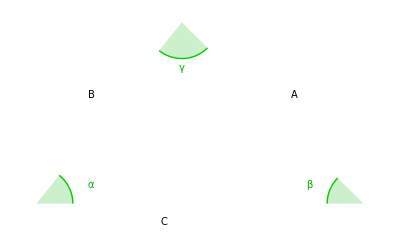
Esercizio 7: |  | 
-Graphics- | A = 2 
B = 3
γ = 60^o
Trovare C | 
Procedimento: |  | 
Applicare il teorema del coseno: | C^2 = ^2 + ^2 - 2 · A ·  · cos() | 
Quindi, sostituendo i valori numerici: | C^2 = ^2 + ^2 - 12 · / =  | 
Da cui:  | C = √ |

```mathematica
Esercizio7[]// Quiet
```

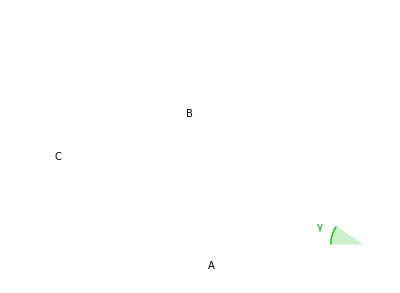
Esercizio 8: |  | 
-Graphics- | A = 24 
C = 12√3
B = 12
Trovare cos(γ) | 
Procedimento: |  | 
Ricorda! C^2 = B^2 + A^2 - 2A·B cos(γ) |  | 
cos(γ) = (SuperscriptBox[B, 2]  +  SuperscriptBox[A, 2]  -  SuperscriptBox[C, 2])/(2  A·B) = (^2 + 576 - 432)/(2 ·) |  | 
Quindi cos(γ) misura: |  | 1/2   | (√3)/2   | -1/2   | -(√3)/2          |

```mathematica
Esercizio8[]// Quiet
```

```mathematica
Esercizio9[]// Quiet
```

Esercizio 9: | 
-Graphics- | Trovare H,
dove H è l'altezza
del campanile
Approssimare il risultato per difetto
tan(^°) = / 
H =  · tan(^°) =

```mathematica
Esercizio10[]// Quiet
```

Esercizio 10: | 
-Graphics- | Trovare α
Approssima il risultato per
difetto alla prima cifra decimale

/(sen(α)) = /(sen(°)) ⟶ sen(α) = / · √/ =

## MA...A COSA SERVE TUTTO QUESTO??

E’ importante sapere che grazie alla trigonometria:

-furono costruiti i primi canocchiali;

```mathematica
ImageResize[Import["Cannocchiale.jpeg"],300]
```

-Graphics-

-fu scoperta la cima più alta del mondo (l'Everest);

```mathematica
ImageResize[Import["Montagna.jpeg"],300]
```

-Graphics-

-è possibile calcolare la distanza tra due punti inaccessibili (fu calcolata così la distanza tra Terra e Luna);

```mathematica
ImageResize[Import["Dist.jpeg"],300]
```

-Graphics-

-si può mappare un territorio (gps),

```mathematica
ImageResize[Import["Triangolazione.jpeg"],300]
```

-Graphics-

## DIFFICOLTA’ RISCONTRATE

- disegnare gli archi per evidenziare gli angoli;
- difficoltà nell’impostare il layout degli esercizi;
- rendere visuale la spiegazione teorica, ma non troppo sintetica.

## BIBLIOGRAFIA E SITOGRAFIA

- Bergamini, Barozzi, Trifone, Manuale blu di matematica 2.0, Volume 3B, Zanichelli , 2016
- http://reference.wolfram.com/language/
- http://mathworld.wolfram.com/

## COMPLIMENTI! PERCORSO COMPLETATO!!